```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
runnumber=100;
threshold=0.0;
max=9999;
```

71

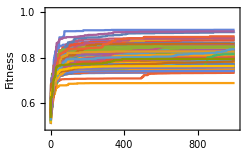

b.eps

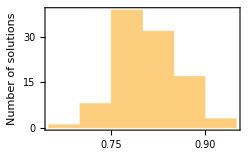

b_hist.eps

```mathematica
exp="C";
maxfit=0.0;
maxind =-1;
allgens={};
allfit={};
bestgen={};
For[i=0, i<runnumber, i++,
file = StringJoin[exp,"/",ToString[i], "/fitness.dat"];
x = Import[file];
y = Transpose[x];
allgens=Append[allgens,y[[2]]];
allfit=Append[allfit,Last[y[[2]]]];
If[Last[y[[2]]]>maxfit,maxfit=Last[y[[2]]];maxind=i;];
If[Last[y[[2]]]>0.95,
file = StringJoin[exp,"/",ToString[i], "/best.gen.dat"];
x = Flatten[Import[file]];
bestgen=Append[bestgen,x];
];
];

maxind
ListLinePlot[Sqrt[allgens],PlotRange->{{-10,1010},{0.49,1.01}},Frame->True,FrameLabel->{"Generations","Fitness"},ImageSize->250]
Export["b.eps",%]
Histogram[Sqrt[allfit],Frame->True,FrameLabel->{"Fitness","Number of solutions"},ImageSize->250]
Export["b_hist.eps",%]
```

```mathematica
DistributionChart[Transpose[bestgen],ChartStyle->"SouthwestColors",ChartElementFunction->"HistogramDensity",Frame->True,AspectRatio->1/10,FrameLabel->{"Parameters","Genotype value"},ImageSize->1200]
Export["Parameters.eps",%]
```

Transpose::nmtx: The first two levels of {} cannot be transposed.

DistributionChart::ldata: Transpose[{}] is not a valid dataset or list of datasets.

General::stop: Further output of DistributionChart::ldata will be suppressed during this calculation.

DistributionChart[Transpose[{}],ChartStyle→SouthwestColors,ChartElementFunction→HistogramDensity,Frame→True,AspectRatio→1/10,FrameLabel→{Parameters,Genotype value},ImageSize→1200]

Parameters.eps